it seems that mathematica already has an internal list of nuclear data yippee!!!!

```mathematica
isotopes = EntityValue["Isotope", {EntityProperty["Isotope","AtomicNumber"], 
	EntityProperty["Isotope","NeutronNumber"], EntityProperty["Isotope","AtomicSymbol"],
	EntityProperty["Isotope","BindingEnergy"]}];
```

make a selection of the nuclides we want to see on the chart

```mathematica
isotopeSelection = Select[isotopes,0<=#[[1]]<=20∧0<#[[2]]<52&];
```

add the format of our chart!

```mathematica
ToBoxes[Superscript[b,a]]//InputForm;
```

prune the data to remove missing/incomplete entries and match atomic number to element

```mathematica
elementAssignment=Union[DeleteCases[isotopeSelection/.{z_, n_, el_, e_}:> Rule[z,el], Rule[a_, Missing["NotAvailable"]]]];

elementAssignment=elementAssignment/.{z_,n_,Missing["NotAvailable"],e_}:>{z,n,z/.rl,e};
finalData=Association[Rule[{#[[1]],#[2]},{#[[3]],#[[4]]}]&/@isotopeSelection];

DeleteCases[
(If[Head[finalData[{#[[1]]-1,#[[2]]}]]=!=Missing,
{#[[1]],#[[2]],finalData[{#[[1]],#[[2]]}][[2]]-finalData[{#[[1]]-1,#[[2]]}][[2]]}])&/@isotopeSelection,Null];
```

plot the nuclide chart

```mathematica
nuclideChart=DisplayForm[RowBox[{"\"\\!\\(\\*SuperscriptBox[\\(\\), \\("<>ToString[#1+#2]<>"\\)]\\)"<>ToString[#3]<>"\""}]]&;

maxBE=Max[#[[4]]/(#[[1]]+#[[2]])&/@isotopeSelection];
color=ColorData["Pastel"][#*0.9/maxBE]&
(*ColorData["Pastel"]*)
```

ColorData[Pastel][(#1 0.9)/maxBE]&

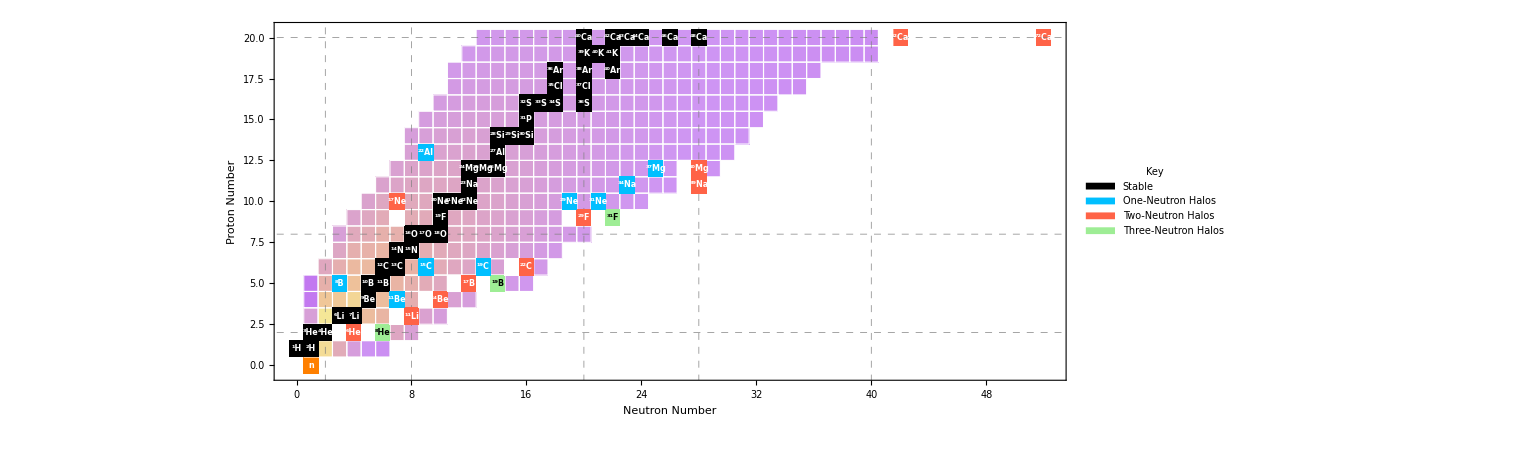

```mathematica
DeepSkyBlue=RGBColor[0,191/255.,1];
PaleGreen=RGBColor[158/255,237/255,149/255];
Tomato=RGBColor[1,99/255,71/255];

Graphics[{Block[{y=#[[1]],x=#[[2]]},{{color[#[[4]]/(#[[1]]+#[[2]])],EdgeForm[White],Rectangle[{x-1/2,y-1/2},{x+1/2,y+1/2}]}(*,Text[nucllab[#[[1]],#[[2]],##[[3]]],{x,y},BaseStyle->Large]*)}]&/@isotopeSelection,{Orange,Thick,Rectangle[{1-1/2,0-1/2},{1+1/2,0+1/2}]},{White,Thick,Text[Style["n",FontSize->8,FontFamily->"Times",Bold],{1.0,0.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{0-1/2,1-1/2},{0+1/2,1+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(1\)]\)H",FontSize->8,FontFamily->"Times",Bold],{0.0,1.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{1-1/2,1-1/2},{1+1/2,1+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(2\)]\)H",FontSize->8,FontFamily->"Times",Bold],{1.0,1.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{1-1/2,2-1/2},{1+1/2,2+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(3\)]\)He",FontSize->8,FontFamily->"Times",Bold],{1.0,2.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{2-1/2,2-1/2},{2+1/2,2+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(4\)]\)He",FontSize->8,FontFamily->"Times",Bold],{2.0,2.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{3-1/2,3-1/2},{3+1/2,3+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(6\)]\)Li",FontSize->8,FontFamily->"Times",Bold],{3.0,3.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{4-1/2,3-1/2},{4+1/2,3+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(7\)]\)Li",FontSize->8,FontFamily->"Times",Bold],{4.0,3.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{5-1/2,4-1/2},{5+1/2,4+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(9\)]\)Be",FontSize->8,FontFamily->"Times",Bold],{5.0,4.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{5-1/2,5-1/2},{5+1/2,5+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(10\)]\)B",FontSize->8,FontFamily->"Times",Bold],{5.0,5.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{6-1/2,5-1/2},{6+1/2,5+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(11\)]\)B",FontSize->8,FontFamily->"Times",Bold],{6.0,5.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{6-1/2,6-1/2},{6+1/2,6+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(12\)]\)C",FontSize->8,FontFamily->"Times",Bold],{6.0,6.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{7-1/2,6-1/2},{7+1/2,6+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(13\)]\)C",FontSize->8,FontFamily->"Times",Bold],{7.0,6.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{7-1/2,7-1/2},{7+1/2,7+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(14\)]\)N",FontSize->8,FontFamily->"Times",Bold],{7.0,7.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{8-1/2,7-1/2},{8+1/2,7+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(15\)]\)N",FontSize->8,FontFamily->"Times",Bold],{8.0,7.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{8-1/2,8-1/2},{8+1/2,8+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(16\)]\)O",FontSize->8,FontFamily->"Times",Bold],{8.0,8.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{9-1/2,8-1/2},{9+1/2,8+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(17\)]\)O",FontSize->8,FontFamily->"Times",Bold],{9.0,8.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{10-1/2,8-1/2},{10+1/2,8+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(18\)]\)O",FontSize->8,FontFamily->"Times",Bold],{10.0,8.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{10-1/2,9-1/2},{10+1/2,9+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(19\)]\)F",FontSize->8,FontFamily->"Times",Bold],{10.0,9.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{10-1/2,10-1/2},{10+1/2,10+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(20\)]\)Ne",FontSize->8,FontFamily->"Times",Bold],{10.0,10.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{11-1/2,10-1/2},{11+1/2,10+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(21\)]\)Ne",FontSize->8,FontFamily->"Times",Bold],{11.0,10.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{12-1/2,10-1/2},{12+1/2,10+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(22\)]\)Ne",FontSize->8,FontFamily->"Times",Bold],{12.0,10.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{12-1/2,11-1/2},{12+1/2,11+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(23\)]\)Na",FontSize->8,FontFamily->"Times",Bold],{12.0,11.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{12-1/2,12-1/2},{12+1/2,12+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(24\)]\)Mg",FontSize->8,FontFamily->"Times",Bold],{12.0,12.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{13-1/2,12-1/2},{13+1/2,12+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(25\)]\)Mg",FontSize->8,FontFamily->"Times",Bold],{13.0,12.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{14-1/2,12-1/2},{14+1/2,12+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(26\)]\)Mg",FontSize->8,FontFamily->"Times",Bold],{14.0,12.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{14-1/2,13-1/2},{14+1/2,13+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(27\)]\)Al",FontSize->8,FontFamily->"Times",Bold],{14.0,13.0},Scaled[{.6,.6}]]},{DeepSkyBlue,Thick,Rectangle[{9-1/2,13-1/2},{9+1/2,13+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(22\)]\)Al",FontSize->8,FontFamily->"Times",Bold],{9.0,13.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{14-1/2,14-1/2},{14+1/2,14+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(28\)]\)Si",FontSize->8,FontFamily->"Times",Bold],{14.0,14.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{15-1/2,14-1/2},{15+1/2,14+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(29\)]\)Si",FontSize->8,FontFamily->"Times",Bold],{15.0,14.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{16-1/2,14-1/2},{16+1/2,14+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(30\)]\)Si",FontSize->8,FontFamily->"Times",Bold],{16.0,14.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{16-1/2,15-1/2},{16+1/2,15+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(31\)]\)P",FontSize->8,FontFamily->"Times",Bold],{16.0,15.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{16-1/2,16-1/2},{16+1/2,16+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(32\)]\)S",FontSize->8,FontFamily->"Times",Bold],{16.0,16.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{17-1/2,16-1/2},{17+1/2,16+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(33\)]\)S",FontSize->8,FontFamily->"Times",Bold],{17.0,16.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{18-1/2,16-1/2},{18+1/2,16+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(34\)]\)S",FontSize->8,FontFamily->"Times",Bold],{18.0,16.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{20-1/2,16-1/2},{20+1/2,16+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(36\)]\)S",FontSize->8,FontFamily->"Times",Bold],{20.0,16.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{18-1/2,17-1/2},{18+1/2,17+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(35\)]\)Cl",FontSize->8,FontFamily->"Times",Bold],{18.0,17.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{20-1/2,17-1/2},{20+1/2,17+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(37\)]\)Cl",FontSize->8,FontFamily->"Times",Bold],{20.0,17.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{18-1/2,18-1/2},{18+1/2,18+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(36\)]\)Ar",FontSize->8,FontFamily->"Times",Bold],{18.0,18.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{20-1/2,18-1/2},{20+1/2,18+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(38\)]\)Ar",FontSize->8,FontFamily->"Times",Bold],{20.0,18.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{22-1/2,18-1/2},{22+1/2,18+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(40\)]\)Ar",FontSize->8,FontFamily->"Times",Bold],{22.0,18.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{20-1/2,19-1/2},{20+1/2,19+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(39\)]\)K",FontSize->8,FontFamily->"Times",Bold],{20.0,19.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{21-1/2,19-1/2},{21+1/2,19+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(40\)]\)K",FontSize->8,FontFamily->"Times",Bold],{21.0,19.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{22-1/2,19-1/2},{22+1/2,19+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(41\)]\)K",FontSize->8,FontFamily->"Times",Bold],{22.0,19.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{20-1/2,20-1/2},{20+1/2,20+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(40\)]\)Ca",FontSize->8,FontFamily->"Times",Bold],{20.0,20.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{22-1/2,20-1/2},{22+1/2,20+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(42\)]\)Ca",FontSize->8,FontFamily->"Times",Bold],{22.0,20.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{23-1/2,20-1/2},{23+1/2,20+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(43\)]\)Ca",FontSize->8,FontFamily->"Times",Bold],{23.0,20.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{24-1/2,20-1/2},{24+1/2,20+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(44\)]\)Ca",FontSize->8,FontFamily->"Times",Bold],{24.0,20.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{26-1/2,20-1/2},{26+1/2,20+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(46\)]\)Ca",FontSize->8,FontFamily->"Times",Bold],{26.0,20.0},Scaled[{.6,.6}]]},{Black,Thick,Rectangle[{28-1/2,20-1/2},{28+1/2,20+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(48\)]\)Ca",FontSize->8,FontFamily->"Times",Bold],{28.0,20.0},Scaled[{.6,.6}]]},{White,Thick,Rectangle[{41-1/2,20-1/2},{41+1/2,20+1/2}]},{Tomato,Thick,Rectangle[{42-1/2,20-1/2},{42+1/2,20+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(62\)]\)Ca",FontSize->8,FontFamily->"Times",Bold],{42.0,20.0},Scaled[{.6,.6}]]},{White,Thick,Rectangle[{51-1/2,20-1/2},{51+1/2,20+1/2}]},{Tomato,Thick,Rectangle[{52-1/2,20-1/2},{52+1/2,20+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(72\)]\)Ca",FontSize->8,FontFamily->"Times",Bold],{52.0,20.0},Scaled[{.6,.6}]]},{White,Thick,Rectangle[{3-1/2,2-1/2},{3+1/2,2+1/2}]},(*{Black,Thick,Text[Style["^5He",FontSize->8,FontFamily->"Times",Bold],{3.0,2.0},Scaled[{.6,.6}]]},*){Tomato,Thick,Rectangle[{4-1/2,2-1/2},{4+1/2,2+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(6\)]\)He",FontSize->8,FontFamily->"Times",Bold],{4.0,2.0},Scaled[{.6,.6}]]},{White,Thick,Rectangle[{5-1/2,2-1/2},{5+1/2,2+1/2}]},(*{Black,Thick,Text[Style["^7He",FontSize->8,FontFamily->"Times",Bold],{5.0,2.0},Scaled[{.6,.6}]]},*){PaleGreen,Thick,Rectangle[{6-1/2,2-1/2},{6+1/2,2+1/2}]},{Black,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(8\)]\)He",FontSize->8,FontFamily->"Times",Bold],{6.0,2.0},Scaled[{.6,.6}]]},{White,Thick,Rectangle[{7-1/2,3-1/2},{7+1/2,3+1/2}]},(*{Black,Thick,Text[Style["^10Li",FontSize->8,FontFamily->"Times",Bold],{7.0,3.0},Scaled[{.6,.6}]]},*){Tomato,Thick,Rectangle[{8-1/2,3-1/2},{8+1/2,3+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(11\)]\)Li",FontSize->8,FontFamily->"Times",Bold],{8.0,3.0},Scaled[{.6,.6}]]},{DeepSkyBlue,Thick,Rectangle[{7-1/2,4-1/2},{7+1/2,4+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(11\)]\)Be",FontSize->8,FontFamily->"Times",Bold],{7.0,4.0},Scaled[{.6,.6}]]},{White,Thick,Rectangle[{9-1/2,4-1/2},{9+1/2,4+1/2}]},(*{Black,Thick,Text[Style["^13Be",FontSize->8,FontFamily->"Times",Bold],{9.0,4.0},Scaled[{.6,.6}]]},*){Tomato,Thick,Rectangle[{10-1/2,4-1/2},{10+1/2,4+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(14\)]\)Be",FontSize->8,FontFamily->"Times",Bold],{10.0,4.0},Scaled[{.6,.6}]]},{DeepSkyBlue,Thick,Rectangle[{3-1/2,5-1/2},{3+1/2,5+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(8\)]\)B",FontSize->8,FontFamily->"Times",Bold],{3.0,5.0},Scaled[{.6,.6}]]},{White,Thick,Rectangle[{11-1/2,5-1/2},{11+1/2,5+1/2}]},(*{Black,Thick,Text[Style["^16B",FontSize->8,FontFamily->"Times",Bold],{11.0,5.0},Scaled[{.6,.6}]]},*){Tomato,Thick,Rectangle[{12-1/2,5-1/2},{12+1/2,5+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(17\)]\)B",FontSize->8,FontFamily->"Times",Bold],{12.0,5.0},Scaled[{.6,.6}]]},{White,Thick,Rectangle[{13-1/2,5-1/2},{13+1/2,5+1/2}]},(*{Black,Thick,Text[Style["^18B",FontSize->8,FontFamily->"Times",Bold],{13.0,5.0},Scaled[{.6,.6}]]},*){PaleGreen,Thick,Rectangle[{14-1/2,5-1/2},{14+1/2,5+1/2}]},{Black,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(19\)]\)B",FontSize->8,FontFamily->"Times",Bold],{14.0,5.0},Scaled[{.6,.6}]]},{DeepSkyBlue,Thick,Rectangle[{9-1/2,6-1/2},{9+1/2,6+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(15\)]\)C",FontSize->8,FontFamily->"Times",Bold],{9.0,6.0},Scaled[{.6,.6}]]},{DeepSkyBlue,Thick,Rectangle[{13-1/2,6-1/2},{13+1/2,6+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(19\)]\)C",FontSize->8,FontFamily->"Times",Bold],{13.0,6.0},Scaled[{.6,.6}]]},{White,Thick,Rectangle[{15-1/2,6-1/2},{15+1/2,6+1/2}]},{Tomato,Thick,Rectangle[{16-1/2,6-1/2},{16+1/2,6+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(22\)]\)C",FontSize->8,FontFamily->"Times",Bold],{16.0,6.0},Scaled[{.6,.6}]]},{White,Thick,Rectangle[{19-1/2,9-1/2},{19+1/2,9+1/2}]},{Tomato,Thick,Rectangle[{20-1/2,9-1/2},{20+1/2,9+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(29\)]\)F",FontSize->8,FontFamily->"Times",Bold],{20.0,9.0},Scaled[{.6,.6}]]},{White,Thick,Rectangle[{21-1/2,9-1/2},{21+1/2,9+1/2}]},{PaleGreen,Thick,Rectangle[{22-1/2,9-1/2},{22+1/2,9+1/2}]},{Black,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(31\)]\)F",FontSize->8,FontFamily->"Times",Bold],{22.0,9.0},Scaled[{.6,.6}]]},{DeepSkyBlue,Thick,Rectangle[{19-1/2,10-1/2},{19+1/2,10+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(29\)]\)Ne",FontSize->8,FontFamily->"Times",Bold],{19.0,10.0},Scaled[{.6,.6}]]},{DeepSkyBlue,Thick,Rectangle[{21-1/2,10-1/2},{21+1/2,10+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(31\)]\)Ne",FontSize->8,FontFamily->"Times",Bold],{21.0,10.0},Scaled[{.6,.6}]]},{DeepSkyBlue,Thick,Rectangle[{23-1/2,11-1/2},{23+1/2,11+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(34\)]\)Na",FontSize->8,FontFamily->"Times",Bold],{23.0,11.0},Scaled[{.6,.6}]]},{DeepSkyBlue,Thick,Rectangle[{25-1/2,12-1/2},{25+1/2,12+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(37\)]\)Mg",FontSize->8,FontFamily->"Times",Bold],{25.0,12.0},Scaled[{.6,.6}]]},{White,Thick,Rectangle[{27-1/2,11-1/2},{27+1/2,11+1/2}]},{Tomato,Thick,Rectangle[{28-1/2,11-1/2},{28+1/2,11+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(39\)]\)Na",FontSize->8,FontFamily->"Times",Bold],{28.0,11.0},Scaled[{.6,.6}]]},{White,Thick,Rectangle[{27-1/2,12-1/2},{27+1/2,12+1/2}]},{Tomato,Thick,Rectangle[{28-1/2,12-1/2},{28+1/2,12+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(40\)]\)Mg",FontSize->8,FontFamily->"Times",Bold],{28.0,12.0},Scaled[{.6,.6}]]},{White,Thick,Rectangle[{7-1/2,9-1/2},{7+1/2,9+1/2}]},{Tomato,Thick,Rectangle[{7-1/2,10-1/2},{7+1/2,10+1/2}]},{White,Thick,Text[Style["\!\(\*SuperscriptBox[\(\), \ \(17\)]\)Ne",FontSize->8,FontFamily->"Times",Bold],{7.0,10.0},Scaled[{.6,.6}]]}},Frame->True,FrameTicksStyle->Directive[Black,Large],FrameLabel->{"Neutron Number","Proton Number"},LabelStyle->Directive[Large,Black],GridLines->{{2,8,20,28,40},{2,8,20,28,40}},GridLinesStyle->Directive[Gray,Thick,Dashed],Epilog->{Inset[SwatchLegend[{Black,DeepSkyBlue,Tomato,PaleGreen},{"Stable","One-Neutron Halos","Two-Neutron Halos","Three-Neutron Halos"},LegendLabel->"Key",LegendMarkerSize->{18,12},LabelStyle->{FontFamily->"Times",FontSize->15}],Scaled[{0.85,0.6}]]}]
```